# Solutions to Select Problems

```mathematica
Quit[]
```

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

"Table of Contents"

## The Postulates of Quantum Mechanics

## Quantum Computation: Overview

The eigenstates of U are the same as those of the Pauli X operator.

```mathematica
U=Rotation[ϕ,S[1,1]]//Elaborate
```

Cos[ϕ/2]-ⅈ S_1^x Sin[ϕ/2]

To see it, take an eigenstate of the Pauli X operator on qubit S[1,$] belonging to the eigenvalue 1.

```mathematica
vec=S[1,6]**Ket[];
vec//LogicalForm
```

(0_S_1)/(√2)+(1_S_1)/(√2)

This confirms that the vector is indeed the intended eigenstate.

```mathematica
U**vec//LogicalForm//TrigToExp//Simplify
```

(ⅇ^(-(ⅈ ϕ)/2) (0_S_1+1_S_1))/(√2)

This checks for the other eigenstate belonging to the eigenvalue -1.

```mathematica
vec=S[1,6]**Ket[S[1]->1];
vec//LogicalForm
```

(0_S_1)/(√2)-(1_S_1)/(√2)

```mathematica
U**vec//LogicalForm//TrigToExp//Simplify
```

(ⅇ^((ⅈ ϕ)/2) (0_S_1-1_S_1))/(√2)

The ancillary qubit takes a relative phase shift depending on in which eigenstate the native qubit is.

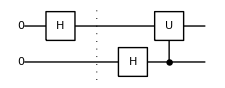

```mathematica
Let[Real,ϕ];
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],"Separator",S[2,6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"]]
```

```mathematica
out=ExpressionFor[qc]//TrigToExp;
KetFactor@out
```

1/2 ⅇ^(-(ⅈ ϕ)/2) (0_S_1+1_S_1)⊗(ⅇ^((ⅈ ϕ)/2) 0_S_2+1_S_2)

Make a basis change to detect it.

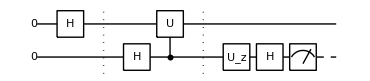

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],"Separator",S[2,6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"],"Separator",Rotation[ϕ/2,S[2,3]],S[2,6],Measurement[S[2,3]]]
```

Finally, check the result.

```mathematica
out=ExpressionFor[qc]//TrigToExp;
LogicalForm[KetFactor@out,S@{1,2}]
```

(ⅇ^(-(ⅈ ϕ)/4) (0_S_10_S_2+1_S_10_S_2))/(√2)

This constructs the desired quantum circuit model.

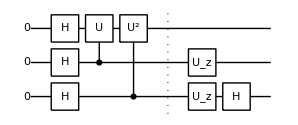

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2,3}],S[{1,2,3},6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"],ControlledU[S[3],Rotation[2ϕ,S[1,1]],"Label"->"U^2"],"Separator",{Rotation[0,S[2,3]],Rotation[Pi/2,S[3,3]]},S[3,6]]
```

```mathematica
out=ExpressionFor[qc]//TrigToExp//Simplify;
KetFactor@out/.ϕ->Pi/2
```

((1/4+ⅈ/4) ⅇ^(-(3 ⅈ π)/4) (0_S_1+1_S_1)⊗(ⅇ^((ⅈ π)/4) 0_S_2+1_S_2)⊗(2 0_S_3))/(√2)

## Virtual Quantum Computers

Here is a quantum circuit model to implement the Pauli X gate based on measurement.

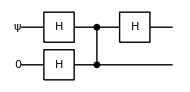

```mathematica
qc=QuantumCircuit[ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]],LogicalForm[Ket[],S@{2}],S[{1,2},6],CZ[S[1],S[2]],S[1,6]]
```

```mathematica
out=Elaborate[qc];
KetFactor[out,S[1]]
```

0_S_1⊗((c_0 ␣)/(√2)+(c_1 1_S_2)/(√2))+1_S_1⊗((c_1 ␣)/(√2)+(c_0 1_S_2)/(√2))

We go further to post-process the output state on the second qubit.

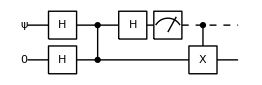

```mathematica
qc1=QuantumCircuit[qc,Measurement[S[1,3]],ControlledU[S[1],S[2,1]]]
```

```mathematica
new=Elaborate[qc1]/.{Conjugate[c[0]]c[0]+Conjugate[c[1]]c[1]->1};
LogicalForm[KetFactor[new,S[1]],S@{1,2}]
```

1_S_1⊗((c_0 0_S_2+c_1 1_S_2)/(√2))

## Quantum Algorithms

Here is a particular classical oracle.

```mathematica
f[0,0]=0
f[0,1]=0
f[1,0]=1
f[1,1]=0
```

0

0

1

0

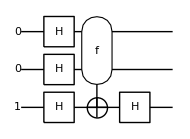

1_S_3⊗(1/2 (0_S_10_S_2+0_S_11_S_2-1_S_10_S_2+1_S_11_S_2))

```mathematica
cc={1,2};
tt={3};
ct=Join[cc,tt];
qc=QuantumCircuit[
LogicalForm[Ket[S[tt]->1],S[ct]],
S[ct,6],
Oracle[f,S@cc,S@tt],
S[tt,6]
]
out=ExpressionFor[qc];
KetFactor[out,S[tt]]//LogicalForm
```

```mathematica
bb=f@@@IntegerDigits[Range[0,2^2],2,2]
```

{0,0,1,0,0}

Here is a particular classical oracle.

```mathematica
f[0,0]={0,1}
f[0,1]={1,0}
f[1,0]={0,1}
f[1,1]={1,1}
```

{0,1}

{1,0}

{0,1}

{1,1}

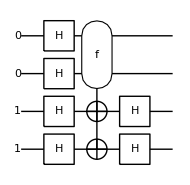

1_S_31_S_4⊗(1/2 (-0_S_10_S_2-0_S_11_S_2-1_S_10_S_2+1_S_11_S_2))

```mathematica
cc={1,2};
tt={3,4};
ct=Join[cc,tt];
qc=QuantumCircuit[
LogicalForm[Ket[S[tt]->1],S[ct]],
S[ct,6],
Oracle[f,S@cc,S@tt],
S[tt,6]
]
out=ExpressionFor[qc];
KetFactor[out,S[tt]]//LogicalForm
```

```mathematica
bb=f@@@IntegerDigits[Range[0,2^2],2,2]
```

{{0,1},{1,0},{0,1},{1,1},{0,1}}

## Decoherence

## Quantum Error-Correction Codes

## Quantum Information Theory